# Non-linear G_eff forms and comparisons

```mathematica
Clear["Global`*"];
```

1. Notes

We use the following definitions which are shared by the ReACT code

We specify G_N in units of [Mpc/M_solar ]

We define y = R_Th/R_i with R_th being the comoving top-hat radius and R_i being the initial top-hat radius. Note that in ReACT SCOL.cpp uses the definition y = (R_Th/R_i-a/a_i)a/a_iwhich we redefine to the usual definition, used here, when feeding to ℱ

2. Constants and background functions

### Newton’s constant, Hubble constant and speed of light

```mathematica
Gnewton = 4.302*10^(-9); (* Units of [Mpc/M_solar (km/s)^2] *)
H0=1/2997.92; (* Units of h/Mpc *)
sofl= 300000; (* Units of km/s *)
```

### Define normalised LCDM Hubble and its scale factor derivative and virial radius in terms of mass

```mathematica
H[a_,Om_]:= Sqrt[Om/a^3 + 1-Om];
DH[a_,Om_]:=-(3 Om)/(2 a^4 √(1-Om+Om/a^3))
Rvir[Om_,Mvir_]:=0.1*(Gnewton*Mvir/(5 Om))^(1/3) (* Halo radius in terms of mass *)
```

### Some fiducial cosmological parameters

```mathematica
Om0 = 0.281; (* Total matter fraction today *) 
scalef = 1; (* Scale factor today *)
```

### Define some fiducial parameters relevant for spherical collapse (virial mass, y initial, y final, initial density fluctuation)

```mathematica
deltai =(0.00003+0.00012)/2; (*Initial density fluctuation *)
Mvir = 10^9; (* Units of M_solar/h *) 
yi = deltai/3;
yf = 1000;
```

### Define some fiducial parameters for modified gravity

```mathematica
Orc=0.25; (*DGP parameter = 1/(2 Subscript[H0r, c])^2 where Subscript[r, c] is the cross over scale*)
f5= 0.00001; (*f(R) parameter : background value of scalar field today *)  
f7= 0.0000001; (*f(R) parameter : background value of scalar field today *)
```

3. Exact forms of  ℱ in DGP and Hu-Sawicki f(R)

## DGP

### Define exact DGP solution : Eq. C6 of 2005.12184

```mathematica
beta[a_,Om_,dof_]:=1+H[a,Om]/Sqrt[dof]*(1+a/3 * DH[a,Om]/H[a,Om])
delta[yh_]:=(1+deltai)/yh^3 -1; 
s3[a_,Om_,yh_,dof_]:=2 Om0 (1+delta[yh])/(9 a^3 beta[a,Om,dof]^2 dof)
```

```mathematica
Fdgp[a_,Om_,yh_,dof_]:=2/(3 beta[a,Om,dof]) * (Sqrt[1+s3[a,Om,yh,dof]]-1)/s3[a,Om,yh,dof]
```

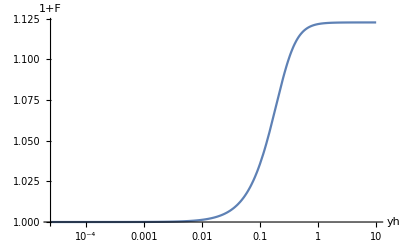

```mathematica
LogLinearPlot[{1+Fdgp[scalef,Om0,yh,Orc]},{yh,yi,10},AxesLabel->{"yh","1+F"}]
```

### Dependence of ℱ on Ω_rc

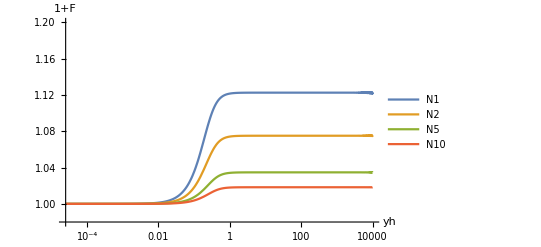

```mathematica
LogLinearPlot[{1+Fdgp[scalef,Om0,yh,0.25],1+Fdgp[scalef,Om0,yh,0.0625],1+Fdgp[scalef,Om0,yh,0.01],1+Fdgp[scalef,Om0,yh,0.0025]},{yh,yi,yf*10},AxesLabel->{"yh","1+F"},PlotRange->{{yi,yf*10},{0.98,1.2}},PlotLegends->{"N1","N2","N5","N10"}]
```

### Dependence of ℱ on redshift

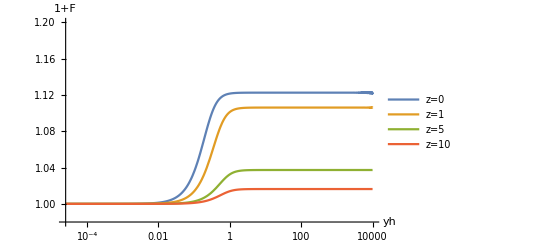

```mathematica
LogLinearPlot[{1+Fdgp[scalef,Om0,yh,Orc],1+Fdgp[1/2,Om0,yh,Orc],1+Fdgp[1/6,Om0,yh,Orc],1+Fdgp[1/11,Om0,yh,Orc]},{yh,yi,yf*10},AxesLabel->{"yh","1+F"},PlotRange->{{yi,yf*10},{0.98,1.2}},PlotLegends->{"z=0","z=1","z=5","z=10"}]
```

## f(R)

### Define exact f(R) Hu-Sawicki solution : Eq. C14 of 2005.12184

```mathematica
Gtild[a_,Om_,y_]:=1/(Om/(y* a)^3 + 4(1-Om))^2;
Of[a_,Om_,yh_,yenv_,Mvir_,dof_]:= dof/H0^2 yh a (3 Om - 4)^2 * (Gtild[a,Om,yenv] -Gtild[a,Om,yh])/(Rvir[Om,Mvir]^2 Om)
```

```mathematica
Ffr[a_,Om_,yh_,yenv_,Mvir_,dof_]:=Min[Of[a,Om,yh,yenv,Mvir,dof]-Of[a,Om,yh,yenv,Mvir,dof]^2+Of[a,Om,yh,yenv,Mvir,dof]^3/3,1/3]
Ffrapprox[a_,Om_,yh_,yenv_,Mvir_,dof_]:=Min[Of[a,Om,yh,yenv,Mvir,dof],1/3]
```

```mathematica
Plot3D[{1+Ffr[scalef,Om0,yh,yenv,Mvir,f5]},{yh,yi,yf},{yenv,yi,yf},AxesLabel->{"yh","ye","1+F"}]
```

-Graphics3D-

```mathematica
Plot3D[{1+Ffr[scalef,Om0,yh,yenv,Mvir*100,f5]},{yh,yi,yf},{yenv,yi,yf},AxesLabel->{"yh","ye","1+F"}]
```

-Graphics3D-

### Dependence of ℱ on environment

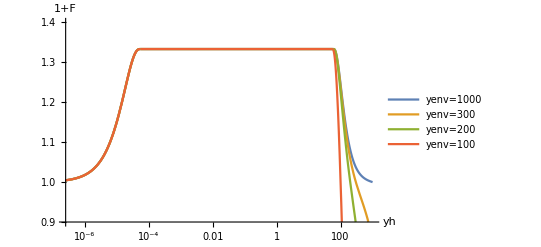

```mathematica
LogLinearPlot[{1+Ffr[scalef,Om0,yh,yf ,Mvir,f5],1+Ffr[scalef,Om0,yh,yf*0.3,Mvir,f5],1+Ffr[scalef,Om0,yh,yf*0.2,Mvir,f5],1+Ffr[scalef,Om0,yh,yf*0.1,Mvir,f5]},{yh,yi*0.01,yf},AxesLabel->{"yh","1+F"},PlotRange->{{yi*0.01,yf},{0.9,1.4}},PlotLegends->{"yenv=1000","yenv=300","yenv=200","yenv=100"}]
```

### Dependence of ℱ on mass

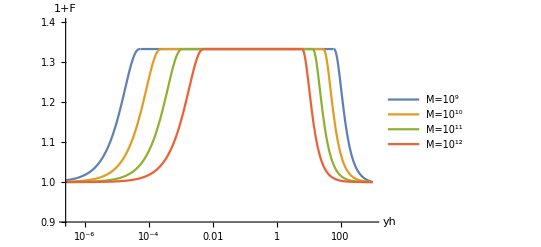

```mathematica
LogLinearPlot[{1+Ffr[scalef,Om0,yh,yf ,Mvir,f5],1+Ffr[scalef,Om0,yh,yf,Mvir*10,f5],1+Ffr[scalef,Om0,yh,yf,Mvir*100,f5],1+Ffr[scalef,Om0,yh,yf,Mvir*1000,f5]},{yh,yi*0.01,yf},AxesLabel->{"yh","1+F"},PlotRange->{{yi*0.01,yf},{0.9,1.4}},PlotLegends->{"M=10^9","M=10^10","M=10^11","M=10^12"}]
```

### Dependence of ℱ on f_R0

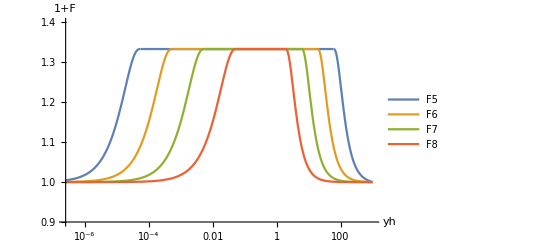

```mathematica
LogLinearPlot[{1+Ffr[scalef,Om0,yh,yf ,Mvir,f5],1+Ffr[scalef,Om0,yh,yf,Mvir,f5/10],1+Ffr[scalef,Om0,yh,yf,Mvir,f5/100],1+Ffr[scalef,Om0,yh,yf,Mvir,f5/1000]},{yh,yi*0.01,yf},AxesLabel->{"yh","1+F"},PlotRange->{{yi*0.01,1000},{0.9,1.4}},PlotLegends->{"F5","F6","F7","F8"}]
```

### Dependence of ℱ on redshift

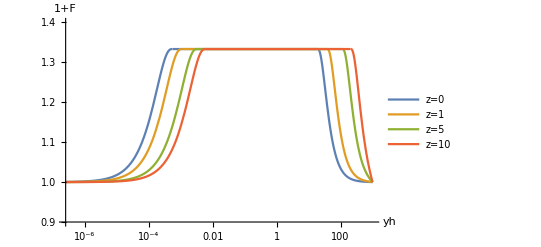

```mathematica
LogLinearPlot[{1+Ffr[scalef,Om0,yh,yf ,Mvir,f5],1+Ffr[1/2,Om0,yh,yf,Mvir,f5],1+Ffr[1/6,Om0,yh,yf,Mvir,f5],1+Ffr[1/11,Om0,yh,yf,Mvir,f5]},{yh,yi*0.01,yf},AxesLabel->{"yh","1+F"},PlotRange->{{yi*0.01,yf},{0.9,1.4}},PlotLegends->{"z=0","z=1","z=5","z=10"}]
```

### Dependence of ℱ on Ω_(m,0)

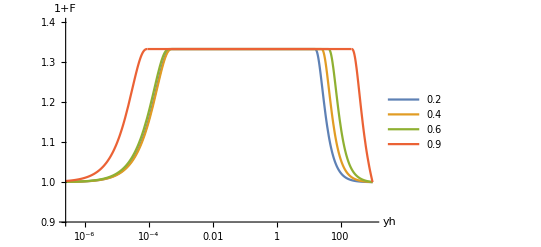

```mathematica
LogLinearPlot[{1+Ffr[scalef,0.2,yh,yf ,Mvir,f5],1+Ffr[1,0.4,yh,yf,Mvir,f5],1+Ffr[1,0.6,yh,yf,Mvir,f5],1+Ffr[1,0.9,yh,yf,Mvir,f5]},{yh,yi*0.01,yf},AxesLabel->{"yh","1+F"},PlotRange->{{yi*0.01,yf},{0.9,1.4}},PlotLegends->{"0.2","0.4","0.6","0.9"}]
```

4. Check exact forms of  ℱ in DGP and f(R) vs PPF ℱ

## Define the PPF effective Newton’s constant: Eq. 5.3 of 1608.00522

Note: we divide G_N by c^2 to get correct units. (M is specified in units of M_solar/h .

```mathematica
y0[a_,yh_,yenv_,Mvir_,par4_,par5_,par6_,par7_]:=p4[a,par4] a ^p5[a,par5](2 Gnewton H0 Mvir/sofl^2)^p6[a,par6](yenv/yh)^p7[a,par7];
apar[a_,par1_,par3_]:=p1[a,par1]/(p1[a,par1]-1) * p3[a,par3];
xm[a_,yh_,yenv_,Mvir_,par1_,par3_,par4_,par5_,par6_,par7_]:=(y0[a,yh,yenv,Mvir,par4,par5,par6,par7]/yh)^apar[a,par1,par3];

Fppf[a_,yh_,yenv_,Mvir_,par1_,par2_,par3_,par4_,par5_,par6_,par7_]:=p1[a,par1]*p2[a,par2]*1/xm[a,yh,yenv,Mvir,par1,par3,par4,par5,par6,par7]*((1+xm[a,yh,yenv,Mvir,par1,par3,par4,par5,par6,par7])^(1/p1[a,par1])-1)
```

## Check PPF vs exact ℱ for DGP : Vainshtein example

### DGP PPF parameters as in Eq.5.9 of 1608.00522

```mathematica
p1[a_,dof_]:= 2;
p2[a_,dof_]:= 1/(3 beta[a,Om0,dof]);
p3[a_,dof_]:= 3/2;
p4[a_,dof_]:= 2 Om0^(1/3) p2[a,dof]^(2/3) /(4 dof)^(1/3);
p5[a_,dof_]:= -1;
p6[a_,dof_]:= 0;
p7[a_,dof_]:= 0;
```

### Plot

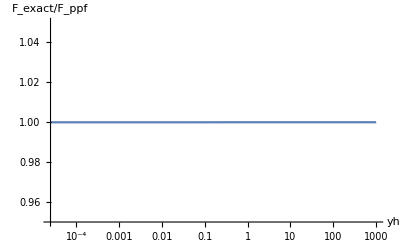

```mathematica
LogLinearPlot[{Fdgp[scalef,Om0,yh,Orc]/Fppf[scalef,yh,yh,Mvir,Orc,Orc,Orc,Orc,Orc,Orc,Orc]},{yh,yi,yf},PlotRange->{{yi,yf},{0.95,1.05}},AxesLabel->{"yh","F_exact/F_ppf"}]
```

## Check PPF vs exact ℱ for Hu-Sawicki f(R) : Chameleon example

### Screened regime : Check with PPF parameters as in Eq.5.6 of 1608.00522. Note BD parameter w = 0

```mathematica
alpha =0.5;
p1[a_,dof_]:= 2
p2[a_,dof_]:= 1/3 ;
p3[a_,dof_]:= (4-alpha)/(1-alpha)
p4[a_,dof_]:=Om0^(1/3)*((Om0+4*(1-Om0))^(1/(alpha-1))*p1[a,dof]*p2[a,dof]/dof)^(1/p3[a,dof]); 
p5[a_,dof_]:=-1;
p6[a_,dof_]:= 2/(3p3[a,dof]); 
p7[a_,dof_]:= 3/(alpha-4);
```

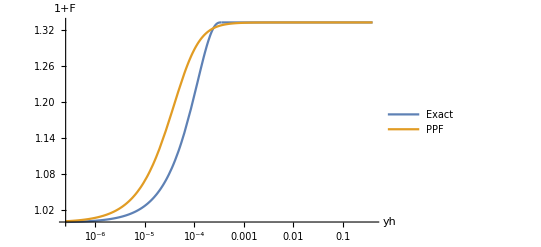

```mathematica
yenv=0.4;
myM=Mvir ;
mya=scalef;
myyenv=1;
LogLinearPlot[{1+Ffr[mya,Om0,yh,myyenv ,myM,f5],1+Fppf[mya,yh,myyenv ,myM,1,1,1,f5,1,1,1]},{yh,yi*0.01,yenv},AxesLabel->{"yh","1+F"},PlotLegends->{"Exact","PPF"}]
```

### Yukawa suppressed regime : Check with PPF parameters as in Eq.5.7 of 1608.00522. Note BD parameter w = 0

```mathematica
alpha =0.5;
p1[a_,dof_]:= 2;
p2[a_,dof_]:= 1/3 ;
p3[a_,dof_]:= -2
p4[a_,dof_]:=Om0^(1/3)*((1-alpha)((4(1-Om0))^(alpha-2)(Om0+4*(1-Om0)))^(1/(alpha-1))*p1[a,dof]*p2[a,dof]/dof)^(1/p3[a,dof]); 
p5[a_,dof_]:=-1; 
p6[a_,dof_]:= 2/(3p3[a,dof]); 
p7[a_,dof_]:= 0;
```

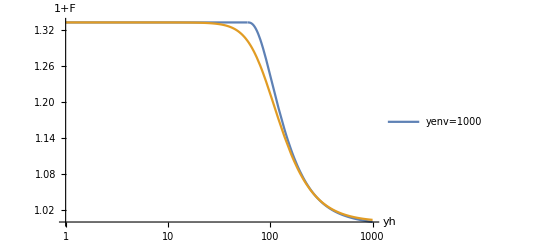

```mathematica
myM=Mvir ;
LogLinearPlot[{1+Ffr[scalef,Om0,yh,yf ,myM ,f5],1+Fppf[scalef,yh,yf  ,myM    ,1,1,1,f5,1,1,1]},{yh,1,yf},AxesLabel->{"yh","1+F"},PlotLegends->{"yenv=1000"}]
```

5. Check exact forms  of  ℱ in DGP and f(R) vs phenomenological ℱ

## Proposed ansatz for ℱ: factorisation of linear G_eff and the error function

### Define linear modifications in DGP and f(R) Hu Sawicki : see Eqs. C3 and C9 of 2005.12184 for example

```mathematica
PI[a_,Om_,k_,fr0_]:=(k/a)^2+((Om+4a^3(1-Om))/a^3)^3/(2 (fr0/H0^2)(3Om-4)^2)
beta[a_,Om_,dof_]:=1+H[a,Om]/Sqrt[dof]*(1+a/3 * DH[a,Om]/H[a,Om])
```

```mathematica
mudgp[a_,Om_,orc_]:=1/3/beta[a,Om,orc]
mufr[a_,Om_,k_,fr0_]:=(k/a)^2/(3PI[a,Om,k,fr0])
```

### Description of 4 free parameters :

k ~ (2π)/R and  R = y_H a R_i/a_i    ⟹ k ~ A/(y_h M_i^(1/3)a) , where A is a constant. By conservation of mass M= M_i for constant density. So we can conclude  k ~ A/(y_h M^(1/3)a)

We found that screening scale goes as inverse size of the top hat or as inverse mass.

p1 gives the screening scale :  p1 = p2 log[R_scr]

p2  gives the mass dependency of the  screening scale :  Erf[ (a yh) (R_scr/R_th)^p2]

p3 gives the environment dependency as a power law: Erf[ (a yh) (R_scr/R_th)^p2  (a yenv)^p3]  .

p4 calibrates the FT of the characteristic scale which depends on halo mass - I think this could be fixed for all theories as its just to calibrate the FT of k...

We do not have any free time dependence - we just convert R to a proper distance by multiplying yh x a. This works  well for a>0.2 (z<4).

For compactness and to keep parameters of order 1,  we write “(R_scr/R_th)^p2  (a yenv)^p3” as 10 to some yenv and R_th dependent power.

```mathematica
myp1[Om_,M_,yenv_,par1_,par2_,par3_]:=par1-par2*Log[Rvir[Om,M]]+par3 Log[yenv]  (* par1, par2 and par3 are also order 1 *) 
myk[a_,Om_,M_,par4_,yh_]:=10^par4/(yh a  Rvir[Om,M]) (* Work with 10^p4 to keep parameters order 1*)
```

### Define the phenomenological function in f(R) and DGP [they vary only in their linear theory form]

```mathematica
Ferfdgp[scalef_,Om_,M_,yh_,yenv_,par1_,par2_,par3_,orc_]:= Erf[ scalef yh  10^myp1[Om,M,yenv* scalef, par1,par2,par3]]mudgp[scalef,Om,orc]  (* No Yukawa suppression so we omit p4 *)
Ferffr[scalef_,Om_,M_,yh_,yenv_,par1_,par2_,par3_,par4_,fr0_]:= Erf[ scalef yh  10^myp1[Om,M,yenv * scalef,par1,par2,par3]]mufr[scalef,Om,myk[scalef,Om,M,par4,scalef yh],fr0]
```

## DGP comparisons

### Fit the free parameter : only the screening scale should matter - no mass or environment dependence, but perhaps some time dependence...

```mathematica
Nk=199;
a1=1;
a2=0.5;
a3=0.2;
a4=0.1;
a5=0.01;
dataa=Table[{yi*Exp[i*Log[yf/yi]/Nk],Fdgp[a1,Om0,yi*Exp[i*Log[yf/yi]/Nk],Orc]},{i,0,Nk}];
datab=Table[{yi*Exp[i*Log[yf/yi]/Nk],Fdgp[a2,Om0,yi*Exp[i*Log[yf/yi]/Nk],Orc]},{i,0,Nk}];datac=Table[{yi*Exp[i*Log[yf/yi]/Nk],Fdgp[a3,Om0,yi*Exp[i*Log[yf/yi]/Nk],Orc]},{i,0,Nk}];datad=Table[{yi*Exp[i*Log[yf/yi]/Nk],Fdgp[a4,Om0,yi*Exp[i*Log[yf/yi]/Nk],Orc]},{i,0,Nk}];datae=Table[{yi*Exp[i*Log[yf/yi]/Nk],Fdgp[a5,Om0,yi*Exp[i*Log[yf/yi]/Nk],Orc]},{i,0,Nk}];
```

```mathematica
sola=FindFit[dataa,Ferfdgp[a1,Om0,Mvir, yh,1,par1,0,0, Orc],{par1},yh]
solb=FindFit[datab,Ferfdgp[a2,Om0,Mvir, yh,1,par1,0,0, Orc],{par1},yh]
solc=FindFit[datac,Ferfdgp[a3,Om0,Mvir, yh,1,par1,0,0, Orc],{par1},yh]
sold=FindFit[datad,Ferfdgp[a4,Om0,Mvir, yh,1,par1,0,0, Orc],{par1},yh]
sole=FindFit[datae,Ferfdgp[a5,Om0,Mvir, yh,1,par1,0,0, Orc],{par1},yh]
```

{par1→0.451112}

{par1→0.492784}

{par1→0.7293}

{par1→0.995563}

{par1→1.97829}

```mathematica
mytab1a={{a1,par1/.sola},{a2 ,par1/.solb},{a3,par1/.solc},{a4,par1/.sold},{a5,par1/.sole}};
myp1a=NonlinearModelFit[mytab1a,a x^b,{a,b},x]
```

FittedModel[0.438694/x^0.328173]

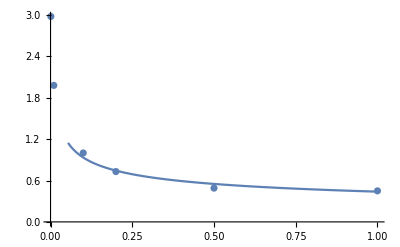

```mathematica
Show[ListPlot[mytab],Plot[myp1a[x],{x,0.001,1}]]
```

Note that we will vary p1 and Ω_rc  in an MCMC so p1 can vary with Ω_rc. The spherical collapse solver requires ℱ to be specified at all redshifts up to the target redshift, and so we may need more parameters if p1 strongly varies with redshift. We will check the reaction to see if this is necessary

### Test fit as a function of redshift (and Ω_rc)

```mathematica
orc = Orc;
orc2 = Orc/10;
```

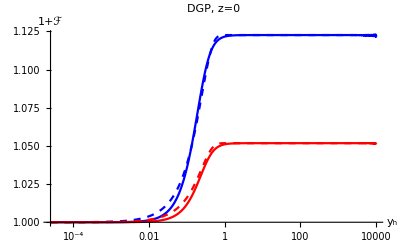

```mathematica
mya=1.;
LogLinearPlot[{1+Fdgp[mya,Om0,yh,orc],1+Ferfdgp[mya,Om0,1, yh,1,par1/.soldgp,0.,0, orc], 1+Fdgp[mya,Om0,yh,orc2],1+Ferfdgp[mya,Om0,1, yh,1,par1/.soldgp,0., 0,orc2]},{yh,yi,yf*10},AxesLabel->{Subscript[y,h],"1+ℱ"},PlotStyle->{{Blue},{Blue,Dashed},Red,{Red,Dashed}},LabelStyle->{FontSize->16,FontFamily->"Times", ,Black,Bold},PlotLabel->"DGP, z=0"]
```

```mathematica
mya=1/2;
LogLinearPlot[{1+Fdgp[mya,Om0,yh,orc],1+Ferfdgp[mya,Om0,1, yh,1,par1/.soldgp,0.,0, orc], 1+Fdgp[mya,Om0,yh,orc2],1+Ferfdgp[mya,Om0,1, yh,1,par1/.soldgp,0.,0, orc2]},{yh,yi,yf*10},AxesLabel->{Subscript[y,h],"1+ℱ"},PlotStyle->{{Blue},{Blue,Dashed},Red,{Red,Dashed}},LabelStyle->{FontSize->16,FontFamily->"Times", ,Black,Bold},PlotLabel->"DGP, z=1"];
```

```mathematica
mya=1/5;
LogLinearPlot[{1+Fdgp[mya,Om0,yh,orc],1+Ferfdgpv3[mya,Om0,1, yh,1,par1/.soldgp,0.,0, orc], 1+Fdgp[mya,Om0,yh,orc2],1+Ferfdgpv3[mya,Om0,1, yh,1,par1/.soldgp,0.,0, orc2]},{yh,yi,yf*10},AxesLabel->{Subscript[y,h],"1+ℱ"},PlotStyle->{{Blue},{Blue,Dashed},Red,{Red,Dashed}},PlotLegends->{"Exact","Phenomenological"},LabelStyle->{FontSize->16,FontFamily->"Times", ,Black,Bold},PlotLabel->"DGP, z=4"];
```

## f(R) comparisons

### Find the mass dependency of the screening scale for F5 for a very large y_env

#### Find the best fit

```mathematica
Nk=199;
mya=scalef;
fofr=f5;
myyenv = 1000;
M1=Mvir*0.1;
M2=Mvir;
M3=Mvir*100;
M4=Mvir*1000;
M5=Mvir*100000;

dataa=Table[{yi*Exp[i*Log[yf/yi]/Nk],Ffr[mya,Om0,yi*Exp[i*Log[yf/yi]/Nk],myyenv,M1,fofr]},{i,0,Nk}];
datab=Table[{yi*Exp[i*Log[yf/yi]/Nk],Ffr[mya,Om0,yi*Exp[i*Log[yf/yi]/Nk],myyenv,M2,fofr]},{i,0,Nk}];
datac=Table[{yi*Exp[i*Log[yf/yi]/Nk],Ffr[mya,Om0,yi*Exp[i*Log[yf/yi]/Nk],myyenv,M3,fofr]},{i,0,Nk}];
datad=Table[{yi*Exp[i*Log[yf/yi]/Nk],Ffr[mya,Om0,yi*Exp[i*Log[yf/yi]/Nk],myyenv,M4,fofr]},{i,0,Nk}];
datae=Table[{yi*Exp[i*Log[yf/yi]/Nk],Ffr[mya,Om0,yi*Exp[i*Log[yf/yi]/Nk],myyenv,M5,fofr]},{i,0,Nk}];
```

```mathematica
sola=FindFit[dataa,Ferffr[mya,Om0,M1,yh,myyenv,par1,0,0,par4,fofr],{par1,par4},yh]
solb=FindFit[datab,Ferffr[mya,Om0,M2,yh,myyenv,par1,0,0,par4,fofr],{par1,par4},yh]
solc=FindFit[datac,Ferffr[mya,Om0,M3,yh,myyenv,par1,0,0,par4,fofr],{par1,par4},yh]
sold=FindFit[datad,Ferffr[mya,Om0,M4,yh,myyenv,par1,0,0,par4,fofr],{par1,par4},yh]
sole=FindFit[datae,Ferffr[mya,Om0,M5,yh,myyenv,par1,0,0,par4,fofr],{par1,par4},yh]
```

{par1→5.21958,par4→0.429466}

{par1→4.60092,par4→0.438547}

{par1→3.28821,par4→0.440118}

{par1→2.62181,par4→0.440114}

{par1→1.28865,par4→0.437841}

```mathematica
mytab1a={{Rvir[Om0,M1],par1/.sola},{Rvir[Om0,M2 ] ,par1/.solb},{Rvir[Om0,M3],par1/.solc},{Rvir[Om0,M4],par1/.sold},{Rvir[Om0,M5],par1/.sole}};
myp1a=NonlinearModelFit[mytab1a,  b+a Log[x],{a,b},x]
```

FittedModel[2.93506-0.855387 Log[x]]

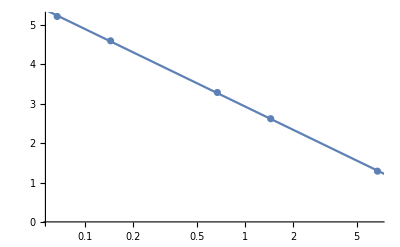

```mathematica
Show[ListLogLinearPlot[mytab1a],LogLinearPlot[myp1a[x],{x,0.01,10}]]
```

```mathematica
p1fitf5 = myp1a[1];
p2fitf5=myp1a[1]-myp1a[Exp[1]];
p4fitf5=((par4/.sola)+(par4/.solb)+(par4/.solc)+(par4/.sold)+(par4/.sole))/5;
```

#### Test the fit for different masses and scale factors

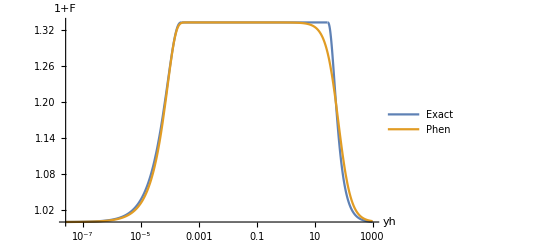

```mathematica
mya=scalef;
myM=Mvir 10;
fofr=f5;
myyenv=1000;
LogLinearPlot[{1+Ffr[mya,Om0,yh,myyenv,myM,fofr],1+Ferffr[mya,Om0,myM,yh,myyenv,p1fitf5,p2fitf5,0,p4fitf5,fofr]},{yh,yi*0.001,yf},AxesLabel->{"yh","1+F"},PlotLegends->{"Exact","Phen"}]
```

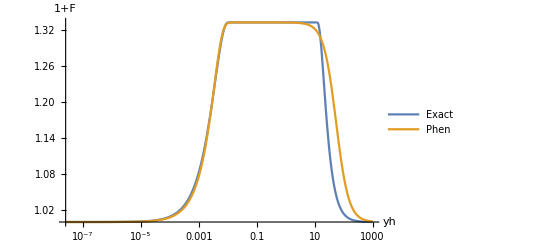

```mathematica
mya=0.5;
myM=Mvir 1000;
fofr=f5;
myyenv=1000;
LogLinearPlot[{1+Ffr[mya,Om0,yh,myyenv,myM,fofr],1+Ferffr[mya,Om0,myM,yh,myyenv,p1fitf5,p2fitf5,0,p4fitf5,fofr]},{yh,yi*0.001,yf},AxesLabel->{"yh","1+F"},PlotLegends->{"Exact","Phen"}]
```

### Find the mass dependency of the screening scale for F7 for a very large y_env

#### Find the best fit

```mathematica
Nk=199;
mya=scalef;
fofr=f7;
myyenv = 1000;
M1=Mvir*0.1;
M2=Mvir;
M3=Mvir*100;
M4=Mvir*1000;
M5=Mvir*100000;

dataa=Table[{yi*Exp[i*Log[yf/yi]/Nk],Ffr[mya,Om0,yi*Exp[i*Log[yf/yi]/Nk],myyenv,M1,fofr]},{i,0,Nk}];
datab=Table[{yi*Exp[i*Log[yf/yi]/Nk],Ffr[mya,Om0,yi*Exp[i*Log[yf/yi]/Nk],myyenv,M2,fofr]},{i,0,Nk}];
datac=Table[{yi*Exp[i*Log[yf/yi]/Nk],Ffr[mya,Om0,yi*Exp[i*Log[yf/yi]/Nk],myyenv,M3,fofr]},{i,0,Nk}];
datad=Table[{yi*Exp[i*Log[yf/yi]/Nk],Ffr[mya,Om0,yi*Exp[i*Log[yf/yi]/Nk],myyenv,M4,fofr]},{i,0,Nk}];
datae=Table[{yi*Exp[i*Log[yf/yi]/Nk],Ffr[mya,Om0,yi*Exp[i*Log[yf/yi]/Nk],myyenv,M5,fofr]},{i,0,Nk}];
```

```mathematica
sola=FindFit[dataa,Ferffr[mya,Om0,M1,yh,myyenv,par1,0,0,par4,fofr],{par1,par4},yh]
solb=FindFit[datab,Ferffr[mya,Om0,M2,yh,myyenv,par1,0,0,par4,fofr],{par1,par4},yh]
solc=FindFit[datac,Ferffr[mya,Om0,M3,yh,myyenv,par1,0,0,par4,fofr],{par1,par4},yh]
sold=FindFit[datad,Ferffr[mya,Om0,M4,yh,myyenv,par1,0,0,par4,fofr],{par1,par4},yh]
sole=FindFit[datae,Ferffr[mya,Om0,M5,yh,myyenv,par1,0,0,par4,fofr],{par1,par4},yh]
```

{par1→3.28821,par4→0.440118}

{par1→2.62181,par4→0.440114}

{par1→1.28865,par4→0.437841}

{par1→0.633992,par4→0.40506}

{par1→-0.515222,par4→0.563698}

```mathematica
mytab1a={{Rvir[Om0,M1],par1/.sola},{Rvir[Om0,M2 ] ,par1/.solb},{Rvir[Om0,M3],par1/.solc},{Rvir[Om0,M4],par1/.sold},{Rvir[Om0,M5],par1/.sole}};
myp1a=NonlinearModelFit[mytab1a,  b+a Log[x],{a,b},x]
```

FittedModel[1.00764-0.831812 Log[x]]

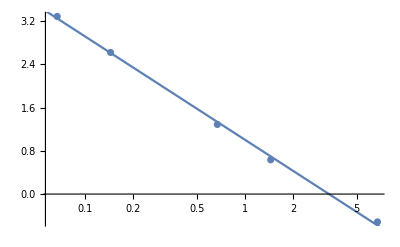

```mathematica
Show[ListLogLinearPlot[mytab1a],LogLinearPlot[myp1a[x],{x,0.01,10}]]
```

```mathematica
p1fitf7 = myp1a[1];
p2fitf7=myp1a[1]-myp1a[Exp[1]];
p4fitf7=((par4/.sola)+(par4/.solb)+(par4/.solc)+(par4/.sold)+(par4/.sole))/5;
```

#### Test the fit for different masses and scale factors

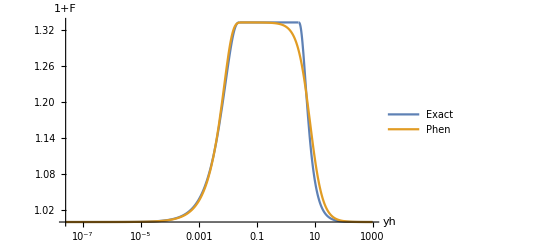

```mathematica
mya=scalef;
myM=Mvir 10;
fofr=f7;
myyenv=1000;
LogLinearPlot[{1+Ffr[mya,Om0,yh,myyenv,myM,fofr],1+Ferffr[mya,Om0,myM,yh,myyenv,p1fitf7,p2fitf7,0,p4fitf7,fofr]},{yh,yi*0.001,yf},AxesLabel->{"yh","1+F"},PlotLegends->{"Exact","Phen"}]
```

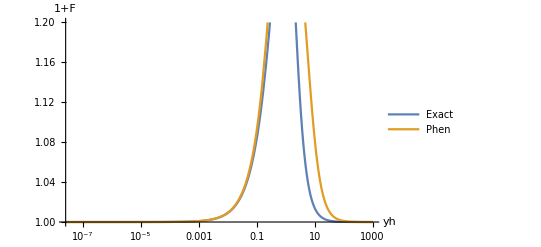

```mathematica
mya=0.5;
myM=Mvir 1000;
fofr=f7;
myyenv=1000;
LogLinearPlot[{1+Ffr[mya,Om0,yh,yf*100,myM,fofr],1+Ferffr[mya,Om0,myM,yh,myyenv,p1fitf7,p2fitf7,0,p4fitf7,fofr]},{yh,yi*0.001,yf},AxesLabel->{"yh","1+F"},PlotLegends->{"Exact","Phen"}]
```

### Find the environment dependency of the screening scale : y_env<1. Note y_h<y_env (halos live in their environment!)

#### Find the best fit - note we drop par4 since we only consider y_h at scales much smaller than the Yukawa suppression scale.

```mathematica
Nk=199;
mya=scalef;
M1=Mvir;
fofr=f5;
Y1=0.55;
Y2=0.4;
Y3=0.3;
Y4=0.1;
Y5=0.001;

dataa=Table[{yi*Exp[i*Log[Y1/yi]/Nk],Ffr[mya,Om0,yi*Exp[i*Log[Y1/yi]/Nk],Y1,M1,fofr]},{i,0,Nk}];
datab=Table[{yi*Exp[i*Log[Y2/yi]/Nk],Ffr[mya,Om0,yi*Exp[i*Log[Y2/yi]/Nk],Y2,M1,fofr]},{i,0,Nk}];
datac=Table[{yi*Exp[i*Log[Y3/yi]/Nk],Ffr[mya,Om0,yi*Exp[i*Log[Y3/yi]/Nk],Y3,M1,fofr]},{i,0,Nk}];
datad=Table[{yi*Exp[i*Log[Y4/yi]/Nk],Ffr[mya,Om0,yi*Exp[i*Log[Y4/yi]/Nk],Y4,M1,fofr]},{i,0,Nk}];
datae=Table[{yi*Exp[i*Log[Y5/yi]/Nk],Ffr[mya,Om0,yi*Exp[i*Log[Y5/yi]/Nk],Y5,M1,fofr]},{i,0,Nk}];
```

```mathematica
sola=FindFit[dataa,Ferffr[mya,Om0,M1,yh,Y1,par1,0,0,0,fofr],{par1},yh]
solb=FindFit[datab,Ferffr[mya,Om0,M1,yh,Y2,par1,0,0,0,fofr],{par1},yh]
solc=FindFit[datac,Ferffr[mya,Om0,M1,yh,Y3,par1,0,0,0,fofr],{par1},yh]
sold=FindFit[datad,Ferffr[mya,Om0,M1,yh,Y4,par1,0,0,0,fofr],{par1},yh]
sole=FindFit[datae,Ferffr[mya,Om0,M1,yh,Y5,par1,0,0,0,fofr],{par1},yh]
```

{par1→4.20985}

{par1→3.81407}

{par1→3.29248}

{par1→0.528558}

{par1→-11.4265}

```mathematica
mytab1a={{Y1,par1/.sola},{Y2 ,par1/.solb},{Y3,par1/.solc},{Y4,par1/.sold},{Y5,par1/.sole}};
myp1a=NonlinearModelFit[mytab1a, b+a Log[x],{a,b},x]
```

FittedModel[6.11079+2.52636 Log[x]]

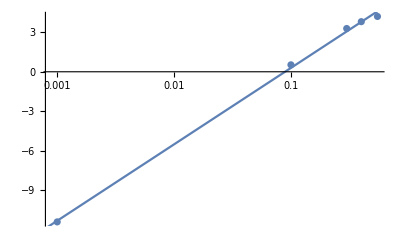

```mathematica
Show[ListLogLinearPlot[mytab1a],LogLinearPlot[myp1a[x],{x,0.00001,1}]]
```

```mathematica
p1fitf5b=myp1a[1]+ p2fitf5 Log[Rvir[Om0,Mvir]] ;
p3fitf5=myp1a[Exp[1]]-myp1a[1];
```

#### Test the fit for different y_env and scale factors

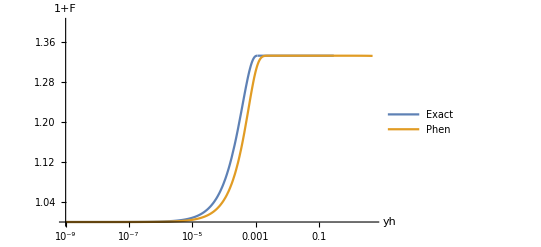

```mathematica
mya=1;
myM=Mvir;
fofr=f5;
myyenv =0.3;
p1fitf5c= Piecewise[{{p1fitf5b,myyenv<0.6},{p1fitf5,myyenv≥0.6}}]; (* Seems to be necessary only for low redshift *)
LogLinearPlot[{1+Ffr[mya,Om0,yh,myyenv,myM,fofr],1+Ferffr[mya,Om0,myM,yh,myyenv,p1fitf5c,p2fitf5,p3fitf5,p4fitf5,fofr]},{yh,10^-9,5},AxesLabel->{"yh","1+F"},PlotLegends->{"Exact","Phen"},PlotRange->{{10^-9,5},{1.,1.4}}]
```

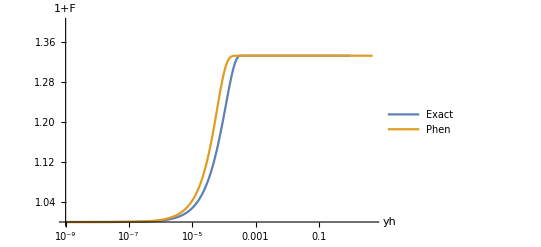

```mathematica
mya=1/2;
myM=Mvir;
fofr=f5;
myyenv =1;
p1fitf5c= Piecewise[{{p1fitf5b,myyenv<0.6},{p1fitf5,myyenv≥0.6}}]; (* Seems to be necessary only for low redshift *)
LogLinearPlot[{1+Ffr[mya,Om0,yh,myyenv,myM,fofr],1+Ferffr[mya,Om0,myM,yh,myyenv,p1fitf5b,p2fitf5,p3fitf5,p4fitf5,fofr]},{yh,10^-9,5},AxesLabel->{"yh","1+F"},PlotLegends->{"Exact","Phen"},PlotRange->{{10^-9,5},{1.,1.4}}]
```

6. Compare all models: Exact, PPF and phenomenological in Hu-Sawicki f(R)

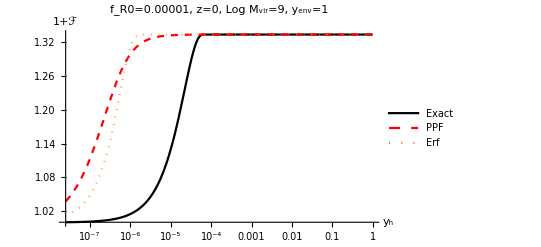

```mathematica
Clear[p1,p2,p3,p4]
alpha =0.5;
p1[a_,dof_]:= 3
p2[a_,dof_]:= 1/3 ;
p3[a_,dof_]:= (4-alpha)/(1-alpha)
p4[a_,dof_]:=Om0^(1/3)*((Om0+4*(1-Om0))^(1/(alpha-1))*p1[a,1]*p2[a,1]/dof)^(1/p3[a,1]); 
p5[a_,dof_]:=-1;
p6[a_,dof_]:= 2/(3p3[a,1]); 
p7[a_,dof_]:= 3/(alpha-4); 
mya=1;
myM=Mvir;
fofr=0.00001;
myyenv=1;
LogLinearPlot[{1+Ffr[mya,Om0,yh,myyenv ,myM,fofr],1+Fppf[mya,yh,myyenv,myM,1,1,1,fofr,1,1,1],1+Ferffr[mya,Om0,myM,yh,myyenv,p1fitf5b,p2fitf5,p3fitf5,p4fitf5,fofr]},{yh,yi*0.001,myyenv*0.99},AxesLabel->{Subscript[y,h],"1+ℱ"},PlotStyle->{{Black},{Red,Dashed},{Orange, Dotted}},LabelStyle->{FontSize->16,FontFamily->"Times", ,Black,Bold},PlotLabel->"f_R0=" <> ToString@fofr <> ", z=" <> ToString@(1/mya-1) <> ", Log M_vir="<> ToString@Log10[myM] <> ", y_env="<> ToString@myyenv <>"",PlotLegends->{"Exact","PPF","Erf"}]
```